## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.2; qscal=1.4; Q=0.9993;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Set::write: Tag Times in (1.38975  - 0.00533667\ ⅈ)\ LeavP1
 is Protected.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Set::write: Tag Times in (1.38975  - 0.00533667\ ⅈ)\ LeavP1
 is Protected.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

Set::write: Tag Times in (1.38975  - 0.00533667\ ⅈ)\ LeavP1
 is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{{15.,1.38975},{14.8,1.38975},{14.6,1.38975},{14.4,1.38975},{14.2,1.38975},{14.,1.38975},{13.8,1.38975},{13.6,1.38975},{13.4,1.38975},{13.2,1.38975},{13.,1.38975},{12.8,1.38975},{12.6,1.38975},{12.4,1.38975},{12.2,1.38975},{12.,1.38975},{11.8,1.38975},{11.6,1.38975},{11.4,1.38975},{11.2,1.38975},{11.,1.38975},{10.8,1.38975},{10.6,1.38975},{10.4,1.38975},{10.2,1.38975},{10.,1.38975},{9.8,1.38975},{9.6,1.38975},{9.4,1.38975},{9.2,1.38975},{9.,1.38975},{8.8,1.38975},{8.6,1.38975},{8.4,1.38975},{8.2,1.38975},{8.,1.38975},{7.8,1.38975},{7.6,1.38975},{7.4,1.38975},{7.2,1.38975},{7.,1.38975},{6.8,1.38975},{6.6,1.38975},{6.4,1.38975},{6.2,1.38975},{6.,1.38975},{5.8,1.38975},{5.6,1.38975},{5.4,1.38975},{5.2,1.38975},{5.,1.38975},{4.8,1.38975},{4.6,1.38975},{4.4,1.38975},{4.2,1.38975},{4.,1.38975},{3.8,1.38975},{3.6,1.38975},{3.4,1.38975},{3.2,1.38975},{3.,1.38975},{2.8,1.38975},{2.6,1.38975},{2.4,1.38975},{2.2,1.38975},{2.,1.38975}}

{{15.,-0.00533667},{14.8,-0.00533667},{14.6,-0.00533667},{14.4,-0.00533667},{14.2,-0.00533667},{14.,-0.00533667},{13.8,-0.00533667},{13.6,-0.00533667},{13.4,-0.00533667},{13.2,-0.00533667},{13.,-0.00533667},{12.8,-0.00533667},{12.6,-0.00533667},{12.4,-0.00533667},{12.2,-0.00533667},{12.,-0.00533667},{11.8,-0.00533667},{11.6,-0.00533667},{11.4,-0.00533667},{11.2,-0.00533667},{11.,-0.00533667},{10.8,-0.00533667},{10.6,-0.00533667},{10.4,-0.00533667},{10.2,-0.00533667},{10.,-0.00533667},{9.8,-0.00533667},{9.6,-0.00533667},{9.4,-0.00533667},{9.2,-0.00533667},{9.,-0.00533667},{8.8,-0.00533667},{8.6,-0.00533667},{8.4,-0.00533667},{8.2,-0.00533667},{8.,-0.00533667},{7.8,-0.00533667},{7.6,-0.00533667},{7.4,-0.00533667},{7.2,-0.00533667},{7.,-0.00533667},{6.8,-0.00533667},{6.6,-0.00533667},{6.4,-0.00533667},{6.2,-0.00533667},{6.,-0.00533667},{5.8,-0.00533667},{5.6,-0.00533667},{5.4,-0.00533667},{5.2,-0.00533667},{5.,-0.00533667},{4.8,-0.00533667},{4.6,-0.00533667},{4.4,-0.00533667},{4.2,-0.00533667},{4.,-0.00533667},{3.8,-0.00533667},{3.6,-0.00533667},{3.4,-0.00533667},{3.2,-0.00533667},{3.,-0.00533667},{2.8,-0.00533667},{2.6,-0.00533667},{2.4,-0.00533667},{2.2,-0.00533667},{2.,-0.00533667}}

-0.00533667

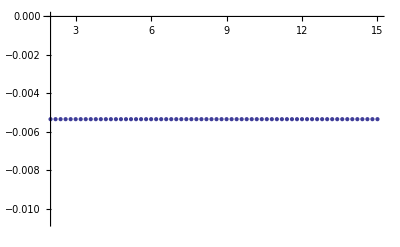

```mathematica
winit=(0.45+0.000005*I);
ie=0;While[ie<66,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=15-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,65}]
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,65}]
Max[t2l[[All,2]]]
ListPlot[{t2l},Axes->True]
```